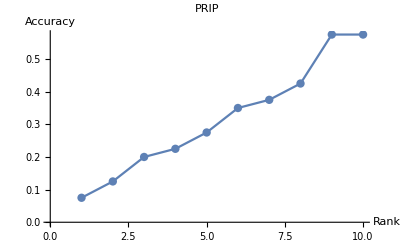

```mathematica
data={0.0750,0.1250,0.2000,0.2250,0.2750,0.3500,0.3750,0.4250,0.5750,0.5750,0.6000,0.6000,0.6250,0.6250,0.6250,0.6500,0.6750,0.6750,0.6750,0.7000,0.7000,0.7250,0.7250,0.7250,0.8000,0.8000,0.8000,0.8000,0.8000,0.8500,0.8500,0.8500,0.8750,0.9000,0.9000,0.9000,0.9250,1.0000,1.0000,1.0000};
data=data[[1;;10]];
p1=ListPlot[data,Joined->True,Mesh->All,AxesLabel->{"Rank","Accuracy"},PlotLabel->"PRIP"]
```

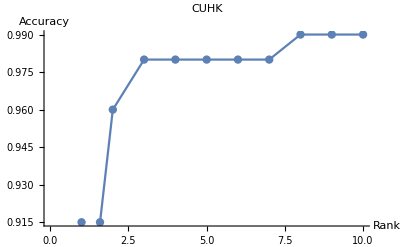

```mathematica
cuhk={0.8500,0.9600,0.9800,0.9800,0.9800,0.9800,0.9800,0.9900,0.9900,0.9900,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000,1.0000};
cuhk=cuhk[[1;;10]];
p2=ListPlot[cuhk,Joined->True,Mesh->All,AxesLabel->{"Rank","Accuracy"},PlotLabel->"CUHK"]
```

```mathematica
Show[p1,p2]
```

-Graphics-